```mathematica
Clear["`*"]
```

# Minus-K Scratch Notebook

## Max Freeman

## Initial Notes

jennifer hoffman stm damping

minus k technology stm vibration isolation scanning tunneling microscope
^ paul weiss -author of papers

Rod Lake @ UW Madison

First: Simulate vibrational spectrum of room
Next: Rod Lake’s articles

airleg/pneumatic damping profile
vibrational damping springs

first: room -> airlegs -> spring -> final
next: room -> airlegs -> minus k spring -> final

Transfer function of airlegs

Transfer function of spring

## Important Links

Air Legs Spec Sheet
Paper on Theory of STM Vibrational Isolation
Less Explicit Paper on Theory of STM Vibrational Isolation

## Terminology

Stress: Force/Area = F/A

Strain: Change in Length / Length = δL/L_0

Stiffness / Modulus: how much energy must be put into the sample to distort it. E = stress/strain

Damping Capacity: a material’s ability to dissipate elastic strain energy (converting to mechanical energy to heat) during mechanical vibration  ⇒ Energy / Volume.

## Images

-Graphics-

-Graphics-
-Graphics-

## Chamberlain Vibrational Data

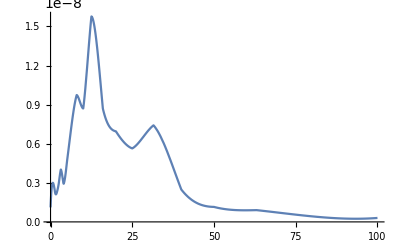

```mathematica
bins = {0,1.25, 1.6, 2, 2.5, 3.15, 4, 5, 6.3, 8, 10, 12.5, 16, 20, 25, 31.5, 40, 50, 63, 80, 100};
pixels = {150,200,190, 196, 210, 230, 210, 238, 266, 285, 278,  315, 278, 264, 251, 268, 200, 152, 137, 90, 69};
f[x_]:= y/.Solve[x== 430/3(Log10[y*10^12]-2),y]⟦1,1⟧//N;
data = Table[f[pixels⟦i⟧],{i, 1, Length[pixels]}];
ifun=Interpolation[Transpose[{bins, data}]];
Plot[ifun[x], {x,0, 100}]
```

## Transfer Functions

Note: This is purely for *vertical* vibrations

### Air Legs

-Graphics-

```mathematica
data = ImageData[Import["C:\\Users\\freem\\Documents\\GitHub\\MinusKModelling\\Resources\\legs_vert_transf.bmp"]];
pixelData={};
For[j=1, j≤Dimensions[data]⟦2⟧, j++,
x={};
For[i =1 , i≤ Dimensions[data]⟦1⟧, i++,
data⟦i,j⟧ = data⟦i,j,1⟧;
If[data⟦i, j⟧≠ 1.,
x = Append[x, i];
];
];
pixelData=Append[pixelData,{j,Dimensions[data]⟦1⟧-Mean[x]}];
]
tAirLeg = {N[0.8*Power[10,Log10[30/0.8]/462*Transpose[pixelData]⟦1⟧]],N[Power[10,4/353 Transpose[pixelData]⟦2⟧-3]]};
```

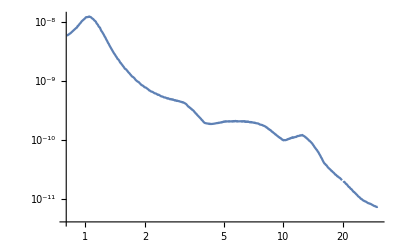

```mathematica
t1 = {tAirLeg⟦1⟧,ifun[tAirLeg⟦1⟧]*tAirLeg⟦2⟧//Quiet};
ListLogLogPlot[Transpose[t1],Joined->True, PlotRange->{{0.8,30}, All}]
```